```mathematica
(* 01 *)
```

{3}

```mathematica
(* 02 *)
Table[RandomInteger[{1,100}],5]
```

{73,49,30,99,66}

```mathematica
(* 03 *)
out = Table[i,{i,1,10}];
RandomSample[out,10]
```

{9,4,10,2,8,3,7,1,5,6}

```mathematica
(* 04 *)
tvSelect[x_]:=QuantityMagnitude[CountryData[x,"TelevisionStations"]]>=100;
largeCountry = Select[CountryData[All],tvSelect]
```

{Australia,Brazil,Canada,China,Denmark,Finland,France,Germany,India,Italy,Japan,Mexico,Netherlands,Philippines,Romania,Russia,Saudi Arabia,South Africa,Spain,Sweden,Switzerland,Thailand,Turkey,Ukraine,United Kingdom,United States}

```mathematica
(* 05 *)
largeCountry = Select[CountryData[All],tvSelect]
```

{Australia,Brazil,Canada,China,Denmark,Finland,France,Germany,India,Italy,Japan,Mexico,Netherlands,Philippines,Romania,Russia,Saudi Arabia,South Africa,Spain,Sweden,Switzerland,Thailand,Turkey,Ukraine,United Kingdom,United States}

```mathematica
(* 06 *)
manyStationsGDPGovDebt = Table[
	{CountryData[country,"GDPPerCapita"],CountryData[country,"GovernmentDebt"]},
	{country,largeCountry}
]
```

{{51812.2 $,5.42309×10^11 $},{6796.84 $,1.73335×10^12 $},{43258.2 $,1.47939×10^12 $},{10500.4 $,5.78589×10^12 $},{61063.3 $,1.17239×10^11 $},{48773.3 $,1.56325×10^11 $},{39030.4 $,2.5059×10^12 $},{46208.4 $,2.34737×10^12 $},{1900.71 $,1.88785×10^12 $},{31676.2 $,2.57926×10^12 $},{39538.9 $,1.15637×10^13 $},{8346.7 $,6.2929×10^11 $},{52397.1 $,4.69973×10^11 $},{3298.83 $,1.31064×10^11 $},{12896.1 $,7.79039×10^10 $},{10126.7 $,2.44001×10^11 $},{20110.3 $,1.18437×10^11 $},{5090.72 $,1.85264×10^11 $},{27063.2 $,1.28835×10^12 $},{52259.3 $,2.20736×10^11 $},{86601.6 $,2.94472×10^11 $},{7189.04 $,1.91214×10^11 $},{8538.17 $,2.43096×10^11 $},{3726.93 $,7.96552×10^10 $},{40284.6 $,2.32967×10^12 $},{63543.6 $,1.53999×10^13 $}}

```mathematica
(* 07 *)
Dimensions[manyStationsGDPGovDebt]
```

{26,2}

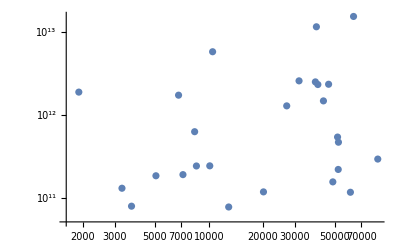

```mathematica
(* 08 *)
ListLogLogPlot[Table[Tooltip[{CountryData[i,"GDPPerCapita"],CountryData[i,"GovernmentDebt"]},i],{i,largeCountry}]]
```

```mathematica
(* 09 *)
Table[Part[manyStationsGDPGovDebt[[i,1]]],{i,1,Length[manyStationsGDPGovDebt]}]
```

{51812.2 $,6796.84 $,43258.2 $,10500.4 $,61063.3 $,48773.3 $,39030.4 $,46208.4 $,1900.71 $,31676.2 $,39538.9 $,8346.7 $,52397.1 $,3298.83 $,12896.1 $,10126.7 $,20110.3 $,5090.72 $,27063.2 $,52259.3 $,86601.6 $,7189.04 $,8538.17 $,3726.93 $,40284.6 $,63543.6 $}

```mathematica
Mean[%81]
```

30078.1 $

```mathematica
(* 10 *)
Correlation[manyStationsGDPGovDebt[[All,1]],manyStationsGDPGovDebt[[All,2]]]
```

0.247475